```mathematica
SetDirectory["C:\\Users\\Georg\\Desktop\\figs"];
<<"CustomTicks.m"
```

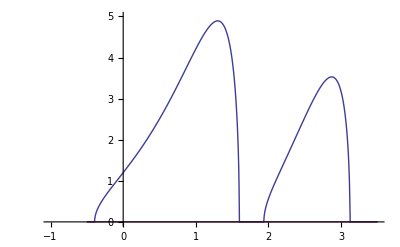

```mathematica
a=.
n=2;
z=1/20;
ϵ=1/2;
λ=0.;
μ=10^a;
h=-1;
ω=Table[-1,{i,1,n}]~Join~Table[+1,{i,1,n}];
g=Table[h μ,{i,1,n}]~Join~Table[-h (1+ϵ) μ,{i,1,n}]/n;
u=Table[(1-n z)/2+z(i-1/2),{i,1,n}]~Join~Table[(1-n z)/2+z(i-1/2),{i,n,1,-1}];
m=Table[KroneckerDelta[i,j] (ω[[i]]+(ϵ μ+λ) u[[i]])-(u[[i]]+u[[j]]) g[[j]],{i,1,2 n},{j,1,2 n}];
pmax=n;
MySort[m_]:=Module[{s},s=Sort[Im[Eigenvalues[m]],Greater];Table[s[[i]],{i,1,pmax}]]
kap=Table[{a}~Join~MySort[m],{a,-0.5,3.5,0.005}];
len=Length[kap];
ListLinePlot[Table[Table[{kap[[i,1]],kap[[i,1+j]]},{i,1,len}],{j,1,pmax}],PlotRange->{{-1,3.5},{0,5}}]
kap20=kap;
```

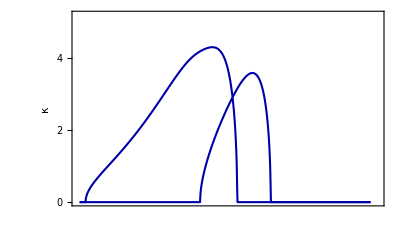

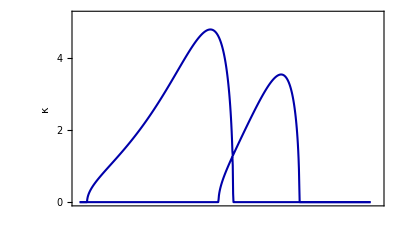

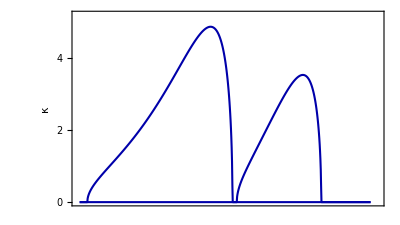

```mathematica
kap=kap2;
pmax=2;
p2=ListLinePlot[Table[Table[{kap[[i,1]],kap[[i,1+j]]},{i,1,Length[kap]}],{j,1,pmax}],PlotRange->{{Log[10,0.3],Log[10,4000]},{0,5.2}},
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},AspectRatio->9/16,
PlotStyle->{{AbsoluteThickness[1.5],Darker[Blue]}},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style[" ",14],Style["κ",14]},
FrameTicks->{LogTicks[-1,4,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[-1,4,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}]
kap=kap5;
pmax=2;
p5=ListLinePlot[Table[Table[{kap[[i,1]],kap[[i,1+j]]},{i,1,Length[kap]}],{j,1,pmax}],PlotRange->{{Log[10,0.3],Log[10,4000]},{0,5.2}},
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},AspectRatio->9/16,
PlotStyle->{{AbsoluteThickness[1.5],Darker[Blue]}},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style[" ",14],Style["κ",14]},
FrameTicks->{LogTicks[-1,4,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[-1,4,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}]
kap=kap10;
pmax=2;
p10=ListLinePlot[Table[Table[{kap[[i,1]],kap[[i,1+j]]},{i,1,Length[kap]}],{j,1,pmax}],PlotRange->{{Log[10,0.3],Log[10,4000]},{0,5.2}},
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},AspectRatio->9/16,
PlotStyle->{{AbsoluteThickness[1.5],Darker[Blue]}},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style[" ",14],Style["κ",14]},
FrameTicks->{LogTicks[-1,4,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[-1,4,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}]
```

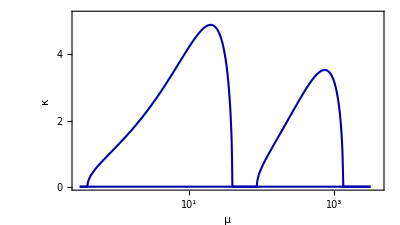

```mathematica
kap=kap20;
pmax=2;
p20=ListLinePlot[Table[Table[{kap[[i,1]],kap[[i,1+j]]},{i,1,Length[kap]}],{j,1,pmax}],PlotRange->{{Log[10,0.3],Log[10,4000]},{0,5.2}},
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},AspectRatio->9/16,
PlotStyle->{{AbsoluteThickness[1.5],Darker[Blue]}},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style["μ",14],Style["κ",14]},
FrameTicks->{LogTicks[-1,4,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[-1,4,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}]
```

```mathematica
Export["discrete2a.eps",p2]
Export["discrete2b.eps",p5]
Export["discrete2c.eps",p10]
Export["discrete2d.eps",p20]
```

discrete2a.eps

discrete2b.eps

discrete2c.eps

discrete2d.eps